1. Задаем начальные данные :

```mathematica
X={π/6,π/4,π/3,π/2}
 f[x_]:=Cot[x]^2 
F=f /@ X
```

{π/6,π/4,π/3,π/2}

{3,1,1/3,0}

```mathematica
n=Length[X]-1
```

3

```mathematica
Do[{Subscript[x, i]=X[[i+1]],Subscript[f, i]=F[[i+1]]},{i,0,n}]
```

```mathematica
Unprotect[Power];0^0:=1;
```

2. Строим алгебраический интерполяционный многочлен:

```mathematica
V=Table[Subscript[d, i,j]=Subscript[x, i]^j,{i,0,n},{j,0,n}]
```

{{1,π/6,π^2/36,π^3/216},{1,π/4,π^2/16,π^3/64},{1,π/3,π^2/9,π^3/27},{1,π/2,π^2/4,π^3/8}}

```mathematica
Do[{Subscript[d, i,n+1]=Subscript[f, i],Subscript[d, n+1,i]=x^i},{i,0,n}]
Subscript[d, n+1,n+1]=0
V1=Table[Subscript[d, i,j],{i,0,n+1},{j,0,n+1}]
```

0

{{1,π/6,π^2/36,π^3/216,3},{1,π/4,π^2/16,π^3/64,1},{1,π/3,π^2/9,π^3/27,1/3},{1,π/2,π^2/4,π^3/8,0},{1,x,x^2,x^3,0}}

```mathematica
P[x_]=-Det[V1]/Det[V]// Expand
```

14-(103 x)/π+(258 x^2)/π^2-(216 x^3)/π^3

3. Строим интерполяционный многочлен с помощью встроенной функции InterpolatingPolynomial:

```mathematica
Tb1=Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}]
P1[x_]=InterpolatingPolynomial[Tb1,x]//Expand
```

{{π/6,3},{π/4,1},{π/3,1/3},{π/2,0}}

14-(103 x)/π+(258 x^2)/π^2-(216 x^3)/π^3

4. Сравниваем интерполяционные многочлены:

```mathematica
P[x]==P1[x]
```

True

5. Проверяем выполнение интерполяционных условий:

```mathematica
Table[P[Subscript[x, i]]==Subscript[f, i],{i,0,n}]
```

{True,True,True,True}

6. Изображаем исходную систему точек и полученный интерполяционный многочлен в одной системе координат:

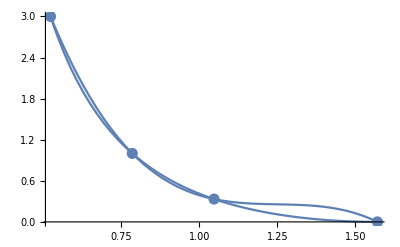

```mathematica
Gr1=ListPlot[Tb1,PlotStyle->{PointSize[0.02]}];
Gr2=Plot[P[x],{x,Subscript[x, 0],Subscript[x, n]}];
Gr3=Plot[f[x],{x,Subscript[x, 0],Subscript[x, n]}];
Show[Gr1,Gr2, Gr3]
```

6. Найти приближенное значение при указанном аргументе и сравнить с точным значением функции:

```mathematica
asdP=P[π/5]//N
```

1.992

```mathematica
absP=Abs[asdP-f[π/5]]
```

0.0975728

```mathematica
dP=absP/asdP*100
```

4.89823

# Задание 2.

Доказать, что тригонометрическая система функций 1, sin(x), cos(x) являются чебышевской на [0,2*Pi].

```mathematica
T = Table[{1,Sin[Subscript[t, i]],Cos[Subscript[t, i]]},{i,0,2}]
Det[T]//TrigToExp//Factor
```

{{1,Sin[t_0],Cos[t_0]},{1,Sin[t_1],Cos[t_1]},{1,Sin[t_2],Cos[t_2]}}

-1/2 ⅈ ⅇ^(-ⅈ t_0-ⅈ t_1-ⅈ t_2) (-ⅇ^(ⅈ t_0)+ⅇ^(ⅈ t_1)) (ⅇ^(ⅈ t_0)-ⅇ^(ⅈ t_2)) (ⅇ^(ⅈ t_1)-ⅇ^(ⅈ t_2))